# Orthogonality and Fourier Analysis with Bessel Functions

In the Trigg Orthogonality notebook, we discussed the general inner product determining the orthogonality of two functions, introduced in equation (1.16), before exploring the orthogonality of sine and cosine. Let's now take a look at the orthogonality of Bessel functions, given by equation (2.32). Once again, these functions do not visually appear to be perpendicular to one another. In the following example, two Bessel functions of the first kind will be shown, with n=1 in red and n=2 in green.

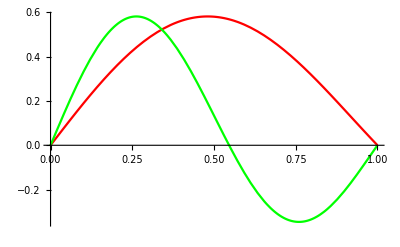

Let's now try graphing the integrand of equation (2.32), where m is the order of the Bessel function, n1 and n2 are the nth zeroes of the Bessel function, and a is our arbitrary starting point. The opaque blue curve represents the integrand of equation (2.32), while the red and green curves represent the individual Bessel functions, which have been initialized to the previously discussed situation with n=1 and n=2. The result of equation (2.32) is also included above the graph.

Here we can clearly see that the area under the curve (the shaded area) totals to zero when we expect the functions to be orthogonal, but that it totals to some nonzero value when the functions are not orthogonal. Try out adjusting the sliders to convince yourself of these conclusions. Let's take a look next at an application of this orthogonality relationship: Fourier Analysis with Bessel Functions.

As discussed previously, Fourier analysis makes use of the orthogonality of a special function to 'pick out' individual terms and find their coefficients. For Bessel functions of the first kind, the Fourier expansion is introduced in equation (2.35), restated below:

f[ρ]=∑_(n=1)^∞ c_mn J[k_[m,n] ρ]

This Fourier-Bessel series is more specific in utility than the Fourier series with sine and cosine, often being used as solutions to differential equations. To get a better sense of using Fourier analysis with Bessel functions, let's look at a few examples.

First, we'll try a very simple function, f(x)=1, for 0<x<1. Using the orthogonality of Bessel functions of the first kind, our coefficients will be:

c_mn=(∫_0^1 x BesselJ[m,BesselJZero[m,n] x]ⅆx)/(1/2 BesselJ[m+1,BesselJZero[m,n]]^2)

Evaluating these expressions, and plugging them into equation (2.35) gives us our Fourier-Bessel series. In the figure, the dotted red curve is our function f(x), while the blue curve is our Fourier-Bessel Series. Using the slider to increase n, you will see that adding in more terms makes our approximation more accurate.

Note that the values for n and m are limited to smaller numbers. This is simply to make sure the expression runs more efficiently, as higher values for n and m take longer to run. As a further note, changing the n and m values for the Fourier-Bessel fit might make the displayed graph disappear or instead display an '$Aborted' message. This just means that the graph is not displayed while Mathematica finishes running calculations, so if you let it run for some time, the graph should eventually appear. If worse comes to worse, you can close and reopen the notebook.

Let's now take a look at another simple function, f(x)=x (represented by the dotted red curve), for 0<x<1, while the Fourier-Bessel Series is represented by the blue curve. We find the following:

Starting from this point, it is clear that we can expand these examples to match the square and sawtooth waveforms from the Trigg Fourier Series notebook.